```mathematica
kcal2kj=QuantityMagnitude@UnitConvert[Quantity[1,"kilocalories"],"kilojoules"];
kj2kcal=1/kcal2kj;
NAvogadro=QuantityMagnitude@Entity["PhysicalConstant","AvogadroConstant"]["Value"];
```

```mathematica
A7=10.610 kj2kcal;
A8=4.048×10^-2 kj2kcal;
β7=0.9630;
β8=2.4192;
z0=2.67;
U[z_]:=A7 Exp[-β7(z-z0)]+A8 Exp[-β8(z-z0)];
```

```mathematica
AS=1.7142 10^-19 NAvogadro 10^-3 kj2kcal
βS=1.2777;
US[z_]:=AS Exp[-βS z];
```

24.6729

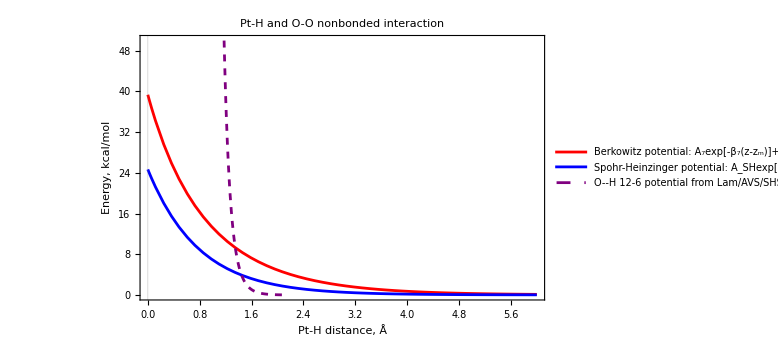

```mathematica
Manipulate[
Plot[{U[z],US[z],362.041/z^12-4.01828/z^6},{z,0,6},
Axes->False,Frame->True,
ImageSize->Large,
FrameLabel->{"Pt-H distance, Å","Energy, kcal/mol"},
FrameStyle->Directive[16,Black,Thickness[Medium]],
PlotStyle->{Red,Blue,{Purple,Dashed}},
PlotRange->{0,50},
GridLines->{{0},None},
PlotLabel->Style["Pt-H and O-O nonbonded interaction\n",Black,16],
PlotLegends->Placed[
{"Berkowitz potential: A_7exp[-β_7(z-z_m)]+A_8exp[-β_8(z-z_m)]",
"Spohr-Heinzinger potential: A_SHexp[-β_SHz]",
"O--H 12-6 potential from Lam/AVS/SHS"
},
{0.6,0.85}]
],
{{R,3.2,"R_DA (Å)"},2.0,5,0.05,Appearance->{"Open","Labeled"}}
]
```